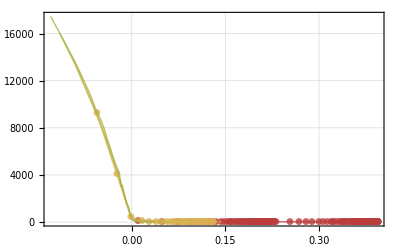

```mathematica
With[
{range = 40000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
Monitor[
Show[
Table[
ListLinePlot[
Sort[Table[N [{magicGraham2[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple calibrated magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples (consecutive only)",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[0.8], ColorData["DarkRainbow"][1/(Log[l])]}
] 
,{l,Min[Map[Length[#[[1]]]&, values]],7}]
],
tuple[[1]]
]
]
]
]
```

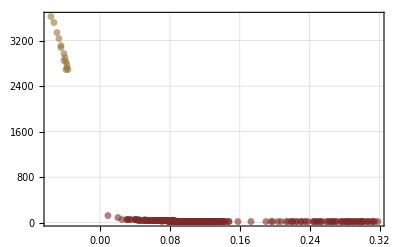

```mathematica
With[
{range = 16000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
Monitor[
Show[
Table[
ListPlot[
Sort[Table[N [{magicGraham2[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple calibrated magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[0.6], Darker[ColorData["DarkRainbow"][1/(Log[l])]]}
] 
,{l,Min[Map[Length[#[[1]]]&, values]],Max[Map[Length[#[[1]]]&, values]]}]
],
tuple[[1]]
]
]
]
]
```